## Hamiltonians

### Definitions

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(* Harper antiperiodic *)
hharpa[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*antiperiodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_]:=hharp[Fibonacci[n-2],Fibonacci[n-1]];
hfiba[n_]:=hharpa[Fibonacci[n-2],Fibonacci[n-1]];
```

## Average exponents

### Typical x, typical eigenfunction

Let us note Ω^n(x) the number of states having a given value of x at step n. One has
Ω^n(x) = Ω(n_m,n_a) with n_m=n x the number of molecular renormalizations, and n_a=n (1-2x)/3 the number of atomic renormalizations, and
Ω(p,q)=2^p((p+q)!)/(p! q!).
When n becomes large, we have Log(Ω^n(x)) ~ f(x) Log(F_n) ~ n Log(ϕ)×f(x) with Log(ϕ)×f(x) = -x Log(3x/2) + (1+x)/3Log(1+x) - (1 - 2x)/3Log(1-2x)
The Log erases a constant factor N. To recover it we simply note that N F_n^(f(x)-1) should be the probability density of x. Thus by the steepest descent method we get
N = √((n σ)/(2 π)) with σ = Log(ϕ) |f''(x_0)|.
The final thing to do to compare asymptotic result for the probability density with Ω^n/F_n is to take the continuous limit. Since there are approximately n/3 values of x at step n, we simply multiply by n/3.

```mathematica
f[x_]:= (-x Log[3x/2] + (1+x)/3 Log[1+x] - (1 - 2x)/3 Log[1-2x])/Log[ω^-1];
```

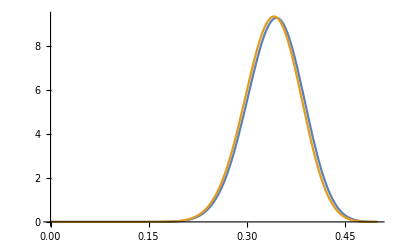

```mathematica
step=80;
(* number of states having value x when n = step *)
compt[x_]:=2^(step x)((step (1+x)/3)!)/((step x)!(step (1-2x)/3)!);
(* exact probability density of x *)
exactfreq[x_]:=step/3 compt[x]/Fibonacci[step];
(* compute variance *)
x0=2(3ω-1)/5; (* this is the value of x that makes f stationnary *)
σ=-f''[x0]*Log[ω^-1];
(* asymptotic probability density of x *)
freq[x_]:=√((step σ)/(2 π))Fibonacci[step]^(f[x]-1);
Plot[{exactfreq[x],freq[x]},{x,0,1/2},PlotRange->All]
```

So, the typical value of x is x_0 such that
f'(x_0) = 0

```mathematica
Solve[f'[x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.341641}}

x_0=2(1-ω^4)/5=2(1-2+3ω)/5=2(3ω-1)/5
We have f(x_0)=1

### Typical exponent

In the large size limit, almost all wavefunctions have x=x_0. Therefore they have the exponent τ_q(x_0). We also compute the average exponent
χ_q=1/F_n Σ_a χ_q(a) = 1/F_n Σ_x Ω(x) χ_q(x).
Thus, we obtain that the average exponent is the exponent of the typical wavefunction:
τ_q=τ_q(x_0)+1-f(x_0) = τ_q(x_0).

This is perhaps too crude a reasoning, since we neglect completely the variance of the probability density of x. More rigorously we write
χ_q = N∫dx F_n^(f(x)-1)F_n^(-τ_q(x))
We let g(x) = - log(ϕ)(f(x)-1) ~ σ/2(x-x_0)^2
and t_q × x = log(ϕ) τ_q(x). (At leading order in ρ τ is linear in x. At second order it is affine in x).
Then [computation to be checked]
χ_q~ e^(-n(t x_0-σt^2/2)) and thus
τ_q=τ_q(x_0)-(σ t_q^2)/(2 log(ϕ))

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBands[n_,ρ_]:=IntBands[n,ρ]=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
Timing[IntBands[19,0.1];]
```

{278.837,Null}

```mathematica
(* averaged q moment of the intensity *)
avqInt[q_,n_,ρ_]:=avqInt[q,n,ρ]=Total[IntBands[n,ρ][[1]]^q,2]/Fibonacci[n];
```

We expect Log (χ^n)_q ~ -τ_q Log F_n , and indeed, Log (χ^n)_q is a linear function of n ~ Log F_n:

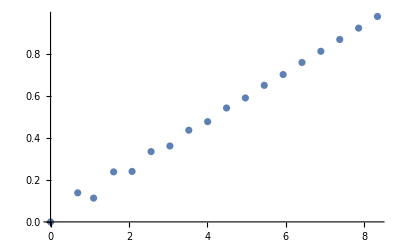

```mathematica
nValues=Range[2,19,1];
avIntN=Map[avqInt[.8,#,0.1]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

```mathematica
glue[Fibonacci[nValues],avIntN]
```

{{1,1.},{2,1.1487},{3,1.12028},{5,1.26959},{8,1.27228},{13,1.39854},{21,1.43646},{34,1.54892},{55,1.61337},{89,1.72205},{144,1.8067},{233,1.91855},{377,2.02012},{610,2.13975},{987,2.25704},{1597,2.38772},{2584,2.52081},{4181,2.66513}}

For large values of q, the 3-periodic behaviour of the Fibonacci numbers (odd, odd, even...) is clearly visible.
It turns out that when F_n is even, there is a gap at E=0, while there is a band when F_n is odd. Since there is an energy level at E=0 for the quasicrystalline chain, we guess that choosing odd approximant is a better idea. If F_n is odd and F_(n-2) as well, then the 2 lateral clusters have also a band in their center. This is perhaps even better.

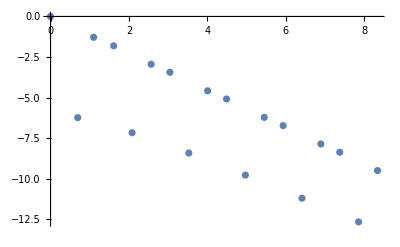

```mathematica
nValues=Range[2,19,1];
avIntN=Map[avqInt[10.,#,0.1]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

For q into the range [0,1) it is safe to disregard the 3-periodicity dependance. Below we compute the slope ie -τ_q for n=13, 16, 19 for different values of q between 0 and 1.

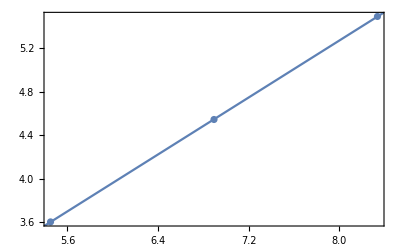

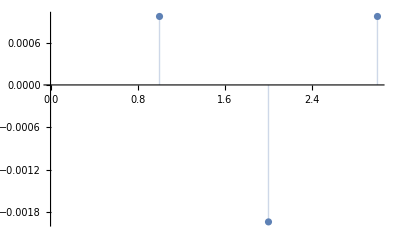

```mathematica
qValues=Range[0,0.9,0.05];
nValues={13,16,19};
avIntN=Map[avqInt[0.2,#,0.1]&,nValues];

dat=glue[Log[Fibonacci[nValues]],Log[avIntN]];
fit=LinearModelFit[dat,n,n];
Show[ListPlot[dat],Plot[fit[n],{n,0,10}],Frame->True]
ListPlot[fit["FitResiduals"], Filling->Axis]
```

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
fits=linFit[#,0.1,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqs=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q] *)
dqs=MapThread[#1/(#2-1)&,{tauqs,qValues}];
(* convert to Subscript[Δ, q] *)
Δqs=MapThread[(#1-(#2-1))&,{tauqs,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

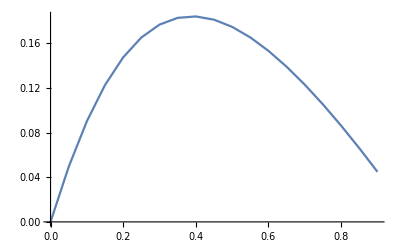

```mathematica
ListPlot[glue[qValues,Δqs],Joined->True]
```

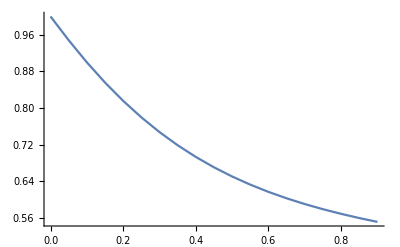

```mathematica
ListPlot[glue[qValues,dqs],Joined->True]
```

It is also possible to derive recursion relations on χ_q^n using the second-order perturbation theory on wavefunctions:
χ_q^n=2(λ/2)^q ω^2 χ_q^(n-2)+(λ')^q ω^3 χ_q^(n-3)
with λ = 1/(1+ρ^2/2), λ'=1/(1+2 ρ^2).

Using that χ_q~F_n^-τ_q, we arrive at an implicit equation on τ_q:

```mathematica
lamb[ρ_,q_]:=2+ρ^(2q)
barlamb[ρ_,q_]:=1+2 ρ^(2q)
gam[ρ_]:=1-ρ^(1.+0.035)/2
(*gam[ρ_]:=1;
gam[ρ_]:=(1/2)(1+ρ^2)*)
lambp[ρ_,q_]:=((1+gam[ρ^q] ρ^(2q)-√(1+(gam[ρ^q] ρ^(2q))^2))/(2gam[ρ^q] ρ^(2q)))^-1;
barlambp[ρ_,q_]:=((√((1+ρ^(2q))^4+4 ρ^(4q))-(1+ρ^(2q))^2)/(2 ρ^4))^-1;
```

```mathematica
eq[q_,τq_,ρ_]:=(2(2+ ρ^(2q)))/lamb[ρ,1.]^q ω^(2(1-τq))+barlamb[ρ,q]/barlamb[ρ,1.]^q ω^(3(1-τq))-1;
(* on prend Subscript[γ, q] = 1 mais Subscript[γ, 1]=1-ρ/2 ; il faudrait aussi Subscript[γ, 0]=0 *)
eqp[q_,τq_,ρ_]:=2(2+ ρ^(2q))/lambp[ρ,1.]^q ω^(2(1-τq))+barlamb[ρ,q]/barlambp[ρ,1.]^q ω^(3(1-τq))-1;
eqtest[q_,τq_,ρ_]:=1/lambp[ρ,1.]^q(2(2+ gam[ρ]^q ρ^(2q))ω^(2(1-τq))+(gam[ρ]^q ρ^(2q))/barlamb[ρ,1.]^q ω^(5(1-τq)))+barlamb[ρ,q]/barlambp[ρ,1.]^q ω^(3(1-τq))-1;
eqref[q_,τq_,ρ_]:=2/((2+ρ^2)^q)ω^(2(1-τq))+1/((1+2 ρ^2)^q)ω^(3(1-τq))-1;
```

```mathematica
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,0.}]
implicitTaup[q_,ρ_]:=τ/.FindRoot[eqp[q,τ,ρ],{τ,0.}]
implicitTauRef[q_,ρ_]:=τ/.FindRoot[eqref[q,τ,ρ],{τ,0.}]
implicitTauTest[q_,ρ_]:=τ/.FindRoot[eqtest[q,τ,ρ],{τ,0.}]
```

```mathematica
Plot[{implicitTaup[q,0.5]/(q-1),implicitTau[q,0.5]/(q-1),implicitTauTest[q,0.5]/(q-1)},{q,0.,5.},PlotStyle->Dashed];
```

The point (q=1,ρ=0) is singular: the function implicitTau has a different value depending on how we approach this point.

For q into the range [0,20] we compute the slope ie -τ_q using the points n=13, 16, 19.

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
nValues={13,16,19};
fits=linFit[#,0.5,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqs=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q] *)
dqs=MapThread[#1/(#2-1)&,{tauqs,qValues}];
(* convert to Subscript[Δ, q] *)
Δqs=MapThread[(#1-(#2-1))&,{tauqs,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

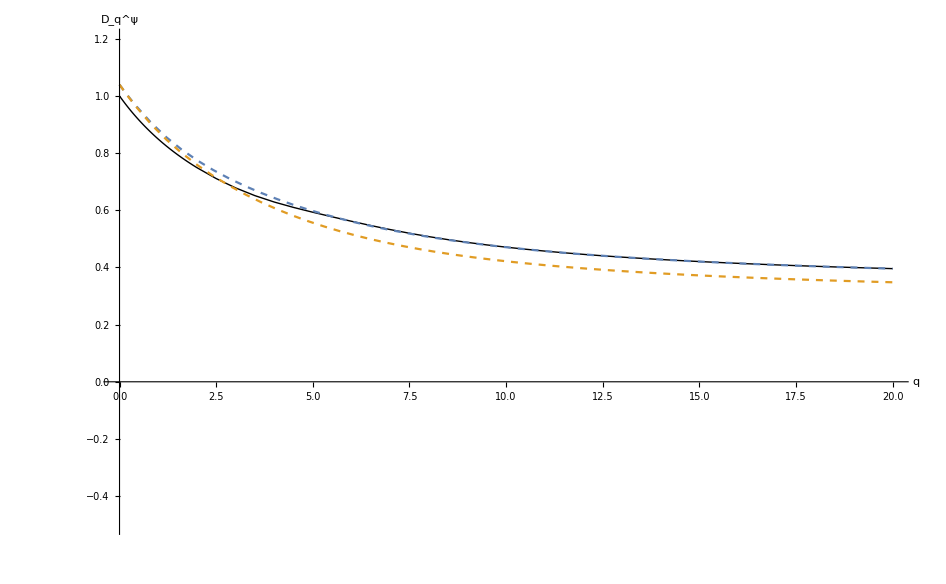

```mathematica
Plot[{implicitTaup[q,0.5]/(q-1),implicitTau[q,0.5]/(q-1)},{q,0.,20.},Prolog->{Thick,Line@glue[qValues,dqs]},PlotRange->{{0.,20},{-0.5,1.2}},AxesLabel->{"q","D_q^ψ"},PlotStyle->Dashed]
```

```mathematica
Export[NotebookDirectory[]<>"data/average_wf_dimension_ρ_10.pdf",%]
```

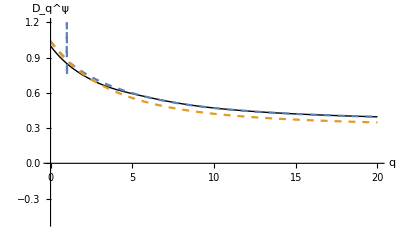

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/average_wf_dimension_ρ_10.pdf

The 3-periodicity is also visible (although much less apparent) for the Harper model using the golden ratio as the irrational (see subsection below).

```mathematica
Inverse[{{2,1},{1,1}}]//MatrixForm
```

(1 | -1
-1 | 2)

```mathematica
Inverse[{{3,2},{2,1}}]//MatrixForm
```

(-1 | 2
2 | -3)

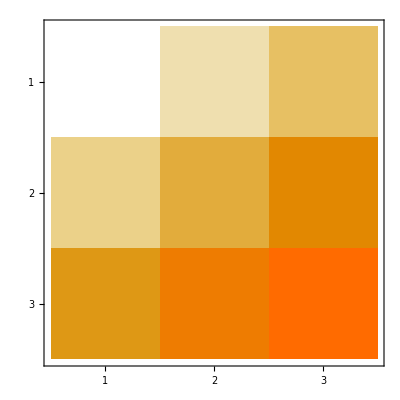

```mathematica
n=4;
L=Fibonacci[n];
t=Table[p Fibonacci[n]+q Fibonacci[n-1],{p,0,L-1,1},{q,0,L-1,1}];
MatrixPlot[t,MaxPlotPoints->Infinity]
```

```mathematica
DuplicateFreeQ[Flatten[t]]
```

True

```mathematica
M0inv=Inverse[{{1,1},{1,0}}]
```

{{0,1},{1,-1}}

```mathematica
Eigensystem[M0inv]
```

{{1/2 (-1-√5),1/2 (-1+√5)},{{1/2 (1-√5),1},{1/2 (1+√5),1}}}

```mathematica
P=Transpose[Eigensystem[M0inv][[2]]];
Diag=DiagonalMatrix[Eigensystem[M0inv][[1]]];
```

```mathematica
Clear[n]
```

```mathematica
P.(Diag^n).Inverse[P].{1,-1}//Expand;
Simplify[%,n>0]
%/.n->6.//Chop
```

{1/5 2^(-1-n) (-(-5+√5) (-1+√5)^n+(-1-√5)^n (5+√5)),1/5 2^(-1-n) ((-1+√5)^n (-5+3 √5)-(-1-√5)^n (5+3 √5))}

{13.,-21.}

```mathematica
13-21ω
```

0.0212862

```mathematica
Fibonacci[n]Fibonacci[n-2]-Fibonacci[n-1]^2//FullSimplify
```

-Cos[n π]

```mathematica
P//MatrixForm
```

(1/2 (1-√5) | 1/2 (1+√5)
1 | 1)

```mathematica
Inverse[P].{1,-1}//Expand//Simplify
```

{1/10 (-5-3 √5),1/10 (-5+3 √5)}

### Harper model

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBandsHarp[n_]:=IntBandsHarp[n]=Block[{vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n]];
{vpa,wfa}=Eigensystem[hfiba[n]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqIntHarp[q_,n_]:=avqIntHarp[q,n]=Total[IntBandsHarp[n][[1]]^q,2]/Fibonacci[n];
```

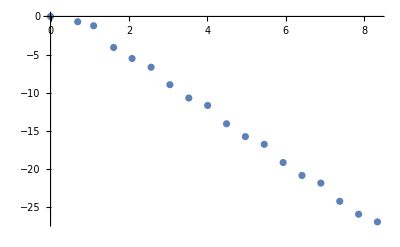

```mathematica
nValues=Range[2,19,1];
avIntN=ParallelMap[avqIntHarp[15.,#]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

For q into the range [0,20] we compute the slope ie -τ_q using the points n=10, 13, 16, 19.

```mathematica
linFitHarp[q_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqIntHarp[q,#]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
qValuesHarp=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
nValuesHarp={10,13,16,19};
fitsHarp=linFitHarp[#,nValuesHarp]&/@qValuesHarp;
```

$Aborted

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqsHarp=-Normal[#["ParameterTable"]][[1,3,2]]&/@fitsHarp;
(* convert to Subscript[D, q] *)
dqsHarp=MapThread[#1/(#2-1)&,{tauqsHarp,qValuesHarp}];
```

Part::partd: Part specification linFitHarp[0., 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

Part::partd: Part specification linFitHarp[0.05, 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

Part::partd: Part specification linFitHarp[0.1, 0.1, {10, 13, 16, 19}]["ParameterTable"] ⟦ 1, 3, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

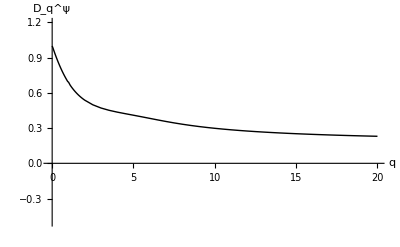

```mathematica
Plot[{},{q,1.1,20.},Prolog->{Thick,Line@glue[qValuesHarp,dqsHarp]},PlotRange->{{-0.1,20},{-0.5,1.2}},AxesLabel->{"q","D_q^ψ"},PlotStyle->Dashed]
```

```mathematica
Export[NotebookDirectory[]<>"../Harper/data/average_wf_dimension.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/../Harper/data/average_wf_dimension.pdf